## Dyskretyzacja filtru

```mathematica
LaunchKernels[48]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local],KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local],KernelObject[21,local],KernelObject[22,local],KernelObject[23,local],KernelObject[24,local],KernelObject[25,local],KernelObject[26,local],KernelObject[27,local],KernelObject[28,local],KernelObject[29,local],KernelObject[30,local],KernelObject[31,local],KernelObject[32,local],KernelObject[33,local],KernelObject[34,local],KernelObject[35,local],KernelObject[36,local],KernelObject[37,local],KernelObject[38,local],KernelObject[39,local],KernelObject[40,local],KernelObject[41,local],KernelObject[42,local],KernelObject[43,local],KernelObject[44,local],KernelObject[45,local],KernelObject[46,local],KernelObject[47,local],KernelObject[48,local]}

```mathematica
data=Table[ Sin[x]+RandomReal[.5],{x,0,2 Pi, 0.05}];
Length@data;
fir={1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Disc
```

```mathematica
ker=FrequencySamplingFilterKernel[fir];
firLen=Length@fir;
signalPerf=ListConvolve[ker,data,firLen];
spectrumPerf=Abs@Fourier[signalPerf, FourierParameters->{-1, 1}];
DiscretizeData[x_,bits_]:=Module[{max},max=Max[x]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
RoundData[x_,bits_]:=Round[x,2^-bits];
SpectrumError[spectrum_]:=Sqrt[Total[Abs[(spectrum-spectrumPerf)]^2]/((Total[Abs[spectrum]^2] ) )];
```

```mathematica
Manipulate[Module[{dataD,kerD,max,spectrumK,spectrumD,spectrumKD,signalK,signalD,signalKD,errK,errD,errKD},
dataD=df[data,n];
kerD=ff[ker,m];

signalK=ListConvolve[kerD,data,firLen];
signalD=ListConvolve[ker,dataD,firLen];
signalKD=ListConvolve[kerD,dataD,firLen];

spectrumK=Abs@Fourier[signalK, FourierParameters->{-1, 1}];
spectrumD=Abs@Fourier[signalD, FourierParameters->{-1, 1}];
spectrumKD=Abs@Fourier[signalKD, FourierParameters->{-1, 1}];

errK=Quiet@SpectrumError[spectrumK];
errD=Quiet@SpectrumError[spectrumD];
errKD=Quiet@SpectrumError[spectrumKD];

Grid[{{Plot[Abs[ListFourierSequenceTransform[ker,x]],{x,0,π},PlotRange->All,PlotLabel->"Filtr",ImageSize->Medium],ListLinePlot[{signalPerf},ImageSize->Medium,PlotRange->Full, PlotLabel->"Bez przybliżeń "],ListLinePlot[{signalD},ImageSize->Medium,PlotRange->Full,PlotLabel->"Przybliżenie sygnału, błąd="<>ToString[errD]]},
{ListLinePlot[{data},ImageSize->Medium,PlotRange->Full,PlotLabel->"sygnał"],ListLinePlot[{signalK},ImageSize->Medium,PlotRange->Full, PlotLabel->"Przybliżenie filtru, błąd=" <>ToString[errK]],
ListLinePlot[{signalKD},ImageSize->Medium,PlotRange->Full,PlotLabel->"Przybliżenie sygnału i filtru, błąd="<>ToString[errKD]]}}]]
,{{n,2,"Przybliżenie sygnału"},0,32,1,Appearance->"Open"},{{m,2,"Przybliżenie filtru "},0,32,1,Appearance->"Open"},{{df,DiscretizeData,"Metoda przybliżenia sygnału"},{DiscretizeData->"Dyskretyzacja na n-bitach",RoundData->"Round[x,2^-n]"}},{{ff,DiscretizeData,"Metoda przybliżenia filtru"},{DiscretizeData->"Dyskretyzacja na n-bitach",RoundData->"Round[x,2^-n]"}}]
```

```mathematica
wyniki=Table[{m,n,Quiet@Log@SpectrumError[Abs@Fourier[ListConvolve[DiscretizeData[ker,m],DiscretizeData[data,n],firLen], FourierParameters->{-1, 1}]]},{m,2,32,2},{n,2,32,2}];
wyniki=Flatten[wyniki,1];
```

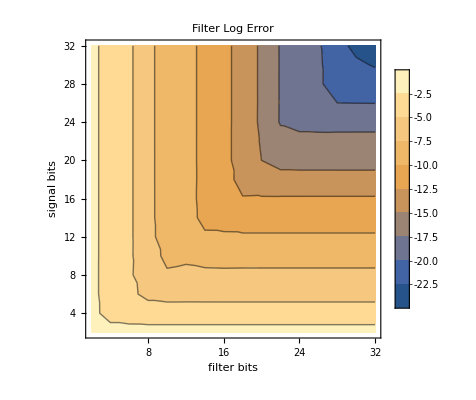

```mathematica
ListContourPlot[wyniki,PlotLegends->Automatic,FrameLabel->{"filter bits","signal bits"},PlotLabel->"Filter Log Error"]
```

## Low-pass

```mathematica
results=ParallelTable[
ωmin=2;
ωmax=20;
filterWidthPercent=arg[[2]];
bits=arg[[3]];
ωprob=2ωmax/filterWidthPercent;
signalRepeats=20;
filterLength=arg[[1]];
{filterLength,filterWidthPercent,bits,Table[
(*bits=32;*)
(*ω=5;*)
noiseLevel=1;
data=Table[Sin[2π ω x]+RandomReal[noiseLevel],{x,0,signalRepeats, 1/(ωprob)}];
fir=Table[1-HeavisideTheta[i-filterWidthPercent*filterLength-0.5],{i,1,filterLength}];
ker=FrequencySamplingFilterKernel[fir];
firLen=Length@fir;
nofilter=Abs[Fourier[data]];
ideal=Abs[Fourier[ListConvolve[ker,data,firLen]]];
discretized=Abs[Fourier[ListConvolve[DiscretizeData[ker,bits],DiscretizeData[data,bits],firLen]]];
all={Rest@nofilter,Rest@ideal,Rest@discretized};
noise={Mean[#[[;;IntegerPart[Length[#]/2.*filterWidthPercent] ]]],MeanDeviation[#[[;;IntegerPart[Length[#]/2.*filterWidthPercent] ]]]}&/@all;
noise2={Mean[#[[IntegerPart[Length[#]/2.*filterWidthPercent]+1;;IntegerPart[Length[#]/2] ]]],MeanDeviation[#[[IntegerPart[Length[#]/2.*filterWidthPercent]+1;;IntegerPart[Length[#]/2] ]]]}&/@all;
peaks=Table[If[Length@#>0,First@#,{-1,0}]&@FindPeaks[all[[i]],1,1,noise[[i,1]]+noise[[i,2]]],{i,1,Length@all}];
correctPeak=peaks[[1,1]];
(*{*){{Abs[peaks[[1,1]]-peaks[[2,1]]],Abs[peaks[[2,1]]-peaks[[3,1]]]},
Log@{all[[2,correctPeak]]/(noise[[2,1]]+noise[[2,2]]),all[[3,correctPeak]]/(noise[[3,1]]+noise[[3,2]])},
Log@{all[[2,correctPeak]]/(noise2[[2,1]]+noise2[[2,2]]),all[[3,correctPeak]]/(noise2[[3,1]]+noise2[[3,2]])}
}(*,ListLogPlot[all,PlotRange->Full,PlotLegends->Placed[{"No filter","Ideal","Discretized"},Top]],
ListLogPlot[EstimatedBackground[#]&/@all,PlotLegends->Placed[{"No filter","Ideal","Discretized"},Top],Joined->True]}*),{ω,ωmin,ωmax,0.5}]},
{arg,Tuples[{(*filterLength,*){(*2,4,*)8,16,32,64,128,256},Range[(*filterWidthPercent,*)0.2,0.9,0.1],(*{bits,*){2,4,6,8,10,12,14,16,18,20}}]}];
```

```mathematica
Export["FIRfilters.mx",results]
```

FIRfilters.mx

```mathematica
len={(*2,4,*)8,16,32,64,128,256};
perc=Range[(*filterWidthPercent,*)0.2,0.9,0.1];
bb={2,4,6,8,10,12,14,16,18,20};
```

```mathematica
results[[1,1;;3]]
```

{8,0.2,2}

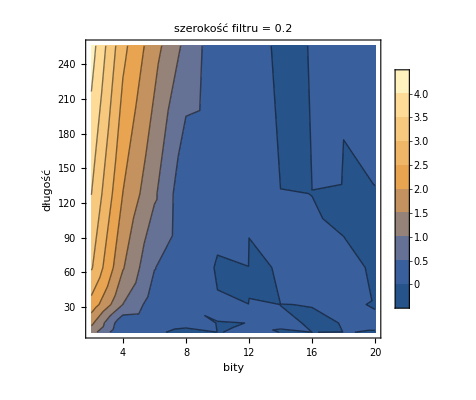
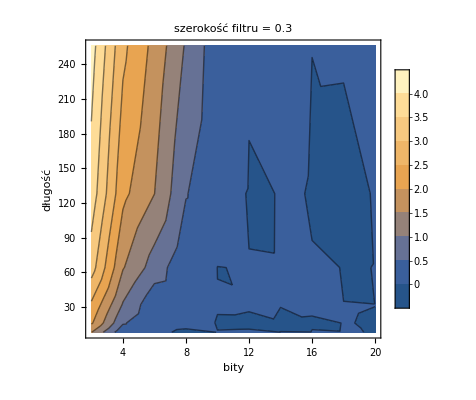
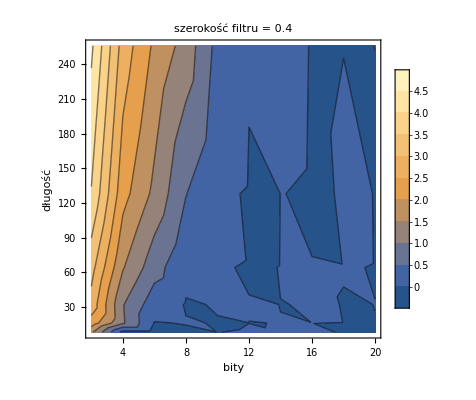
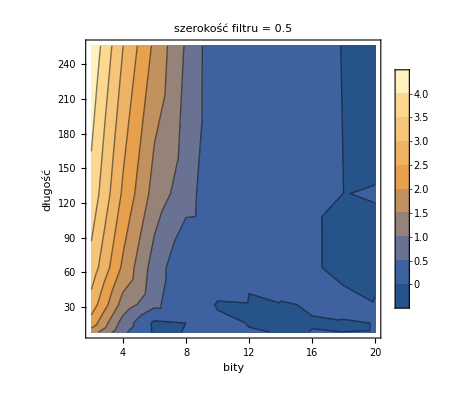
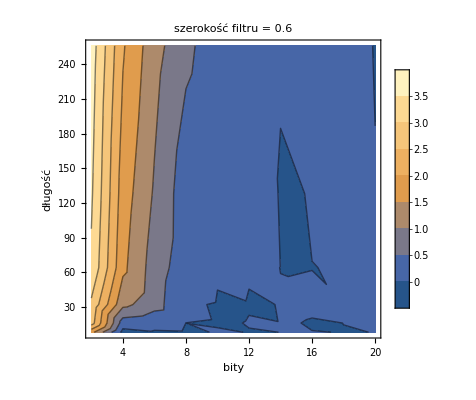
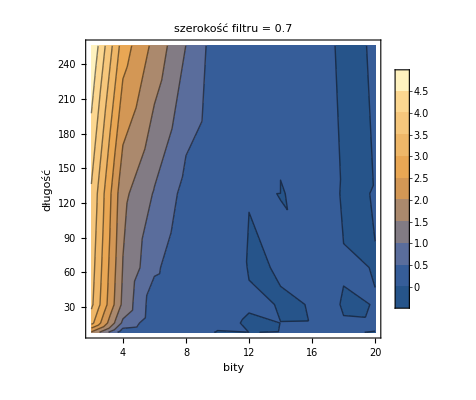
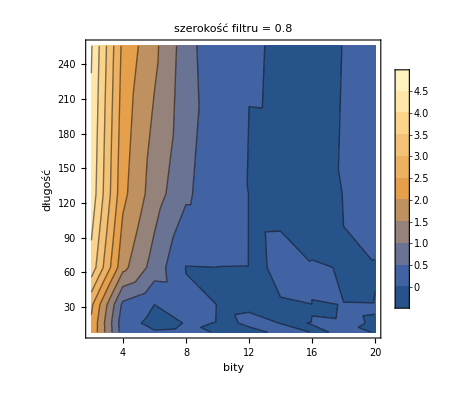
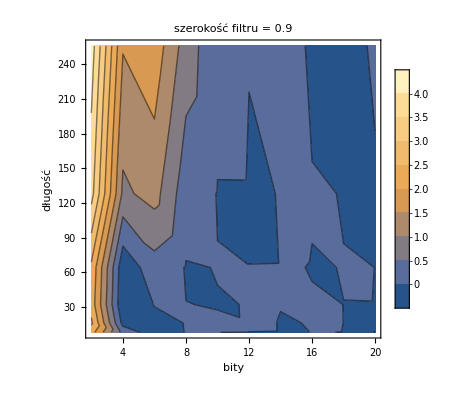
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[perSNR=Select[results,#[[2]]==i&][[All,{1,3,4}]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@perSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"bity","długość"},PlotLabel->"szerokość filtru = "<>ToString[i]],{i,perc}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

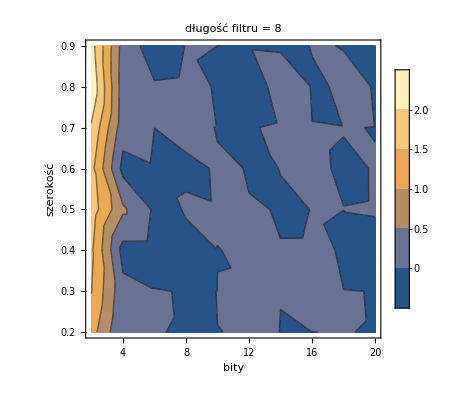
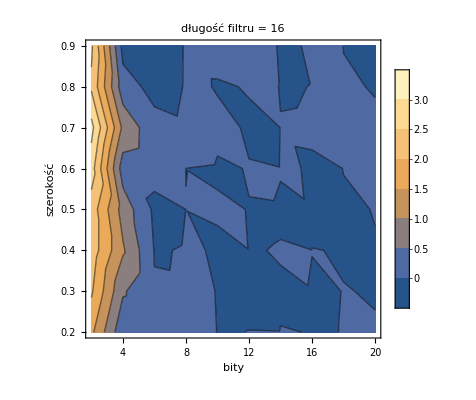
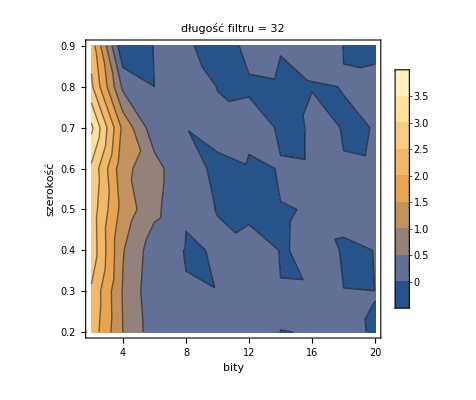
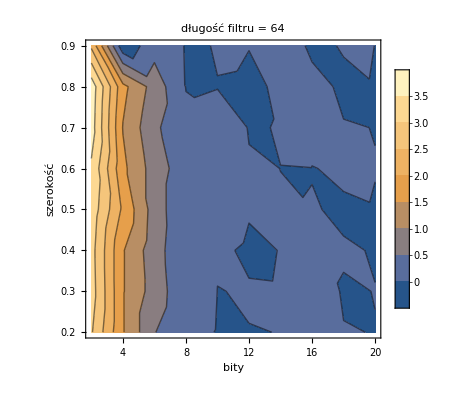
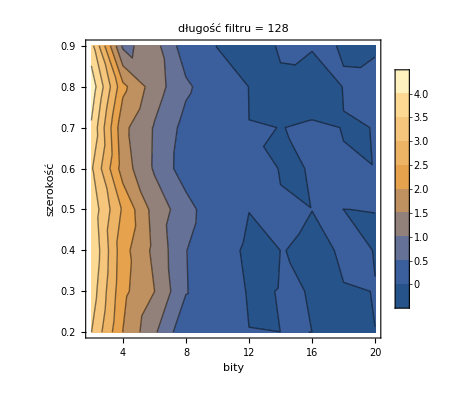
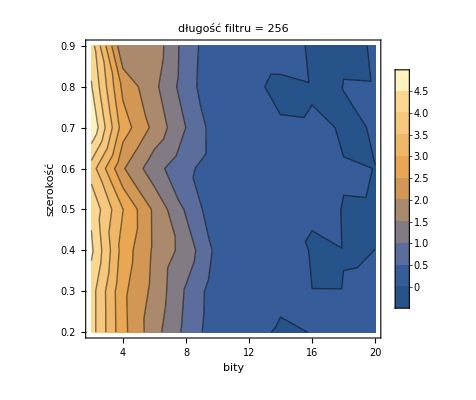
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[lenSNR=Select[results,#[[1]]==i&][[All,2;;]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@lenSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"bity","szerokość"},PlotLabel->"długość filtru = "<>ToString[i]],{i,len}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

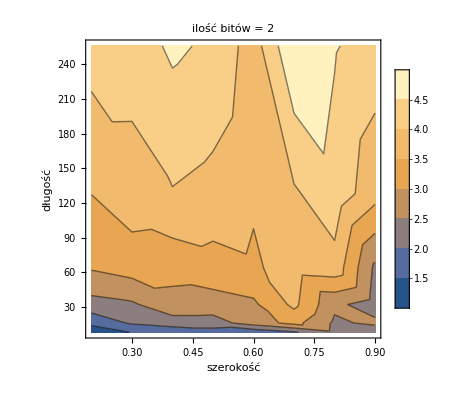
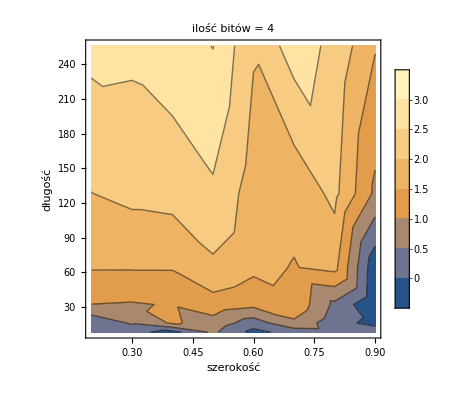
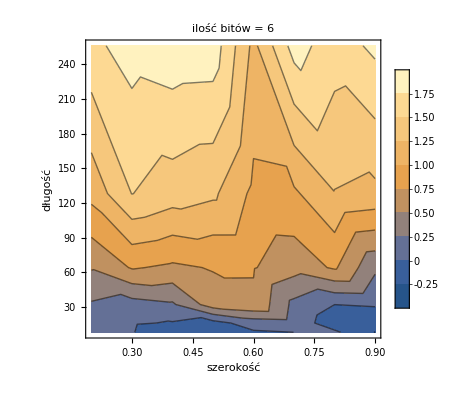
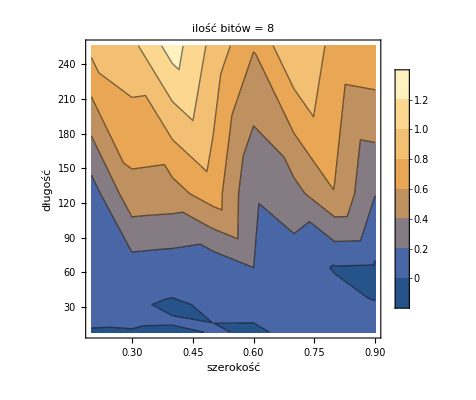
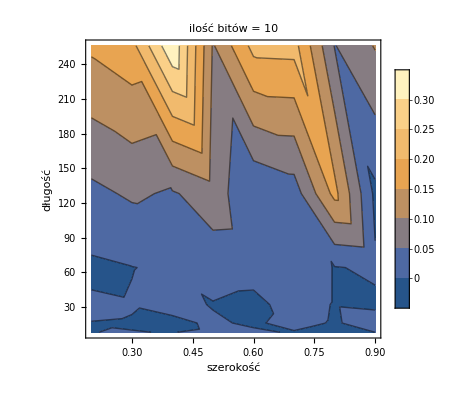
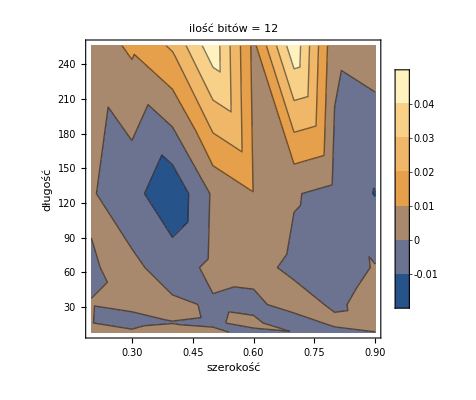
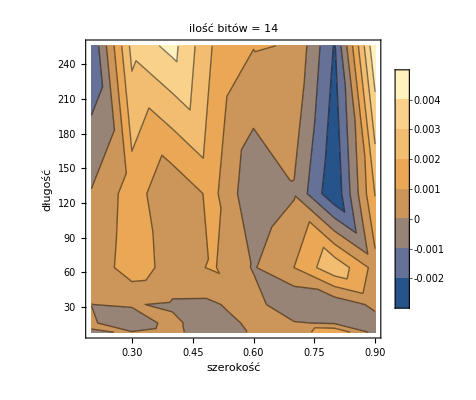
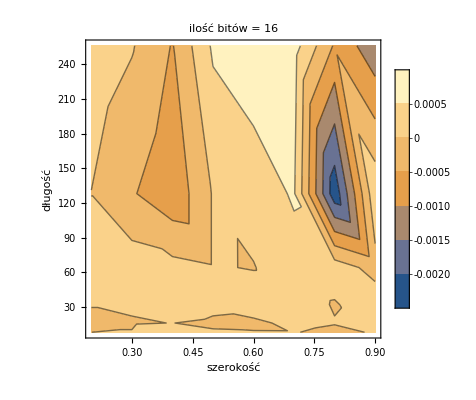
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[perSNR=Select[results,#[[3]]==i&][[All,{1,2,4}]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@perSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"szerokość","długość"},PlotLabel->"ilość bitów = "<>ToString[i]],{i,bb}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

```mathematica
spectrumPerf=Abs@Fourier[signalPerf, FourierParameters->{-1, 1}];
DiscretizeData[x_,bits_]:=Module[{max},max=Max[x]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] (*max/(Power[2,bits-1]-1)*) &/@x];
RoundData[x_,bits_]:=Round[x,2^-bits];
SpectrumError[spectrum_]:=Sqrt[Total[Abs[(spectrum-spectrumPerf)]^2]/((Total[Abs[spectrum]^2] ) )];
```

## Mid-pass

```mathematica
results=ParallelTable[
ωmin=2;
ωmax=20;
filterWidthPercent=arg[[2]]/2.0;
bits=arg[[3]];
ωprob=2ωmax/filterWidthPercent;
signalRepeats=20;
filterLength=arg[[1]];
{filterLength,filterWidthPercent,bits,Table[
(*bits=32;*)
(*ω=5;*)
noiseLevel=1;
data=Table[Sin[2π ω x]+RandomReal[noiseLevel],{x,0,signalRepeats, 1/(ωprob)}];
fir=Floor[Table[1/2HeavisideTheta[i-filterWidthPercent*filterLength+0.5]+1/2HeavisideTheta[filterLength-filterWidthPercent*filterLength-i+1.5],{i,1,filterLength}]];
ker=FrequencySamplingFilterKernel[fir];
firLen=Length@fir;
nofilter=Abs[Fourier[data]];
ideal=Abs[Fourier[ListConvolve[ker,data,firLen]]];
discretized=Abs[Fourier[ListConvolve[DiscretizeData[ker,bits],DiscretizeData[data,bits],firLen]]];
all={Rest@nofilter,Rest@ideal,Rest@discretized};

noise={Mean[# Floor[Table[1/2HeavisideTheta[i-filterWidthPercent*Length[#]+0.5]+1/2HeavisideTheta[Length[#]-filterWidthPercent*Length[#]-i+1.5],{i,1,Length[#]}]] ],MeanDeviation[# Floor[Table[1/2HeavisideTheta[i-filterWidthPercent*Length[#]+0.5]+1/2HeavisideTheta[Length[#]-filterWidthPercent*Length[#]-i+1.5],{i,1,Length[#]}]] ]}&/@all;
noise2={Mean[#(1-Floor[Table[1/2HeavisideTheta[i-filterWidthPercent*Length[#]+0.5]+1/2HeavisideTheta[Length[#]-filterWidthPercent*Length[#]-i+1.5],{i,1,Length[#]}]] )],MeanDeviation[#(1-Floor[Table[1/2HeavisideTheta[i-filterWidthPercent*Length[#]+0.5]+1/2HeavisideTheta[Length[#]-filterWidthPercent*Length[#]-i+1.5],{i,1,Length[#]}]])]}&/@all;
peaks=Table[If[Length@#>0,First@#,{-1,0}]&@FindPeaks[all[[i]],1,1,noise[[i,1]]+noise[[i,2]]],{i,1,Length@all}];
correctPeak=peaks[[1,1]];
(*{*){{Abs[peaks[[1,1]]-peaks[[2,1]]],Abs[peaks[[2,1]]-peaks[[3,1]]]},
Log@{all[[2,correctPeak]]/(noise[[2,1]]+noise[[2,2]]),all[[3,correctPeak]]/(noise[[3,1]]+noise[[3,2]])},
Log@{all[[2,correctPeak]]/(noise2[[2,1]]+noise2[[2,2]]),all[[3,correctPeak]]/(noise2[[3,1]]+noise2[[3,2]])}
}(*,ListLogPlot[all,PlotRange->Full,PlotLegends->Placed[{"No filter","Ideal","Discretized"},Top]],
ListLogPlot[EstimatedBackground[#]&/@all,PlotLegends->Placed[{"No filter","Ideal","Discretized"},Top],Joined->True]}*),{ω,ωmin,ωmax,0.5}]},
{arg,Tuples[{(*filterLength,*)len,perc,(*{bits,*)bb}]}];
```

```mathematica
Export["FIRfiltersMid.mx",results]
```

FIRfilters.mx

```mathematica
len={(*2,4,*)8,16,32,64,128,256};
perc=Range[(*filterWidthPercent,*)0.2,0.8,0.1];
bb={2,4,6,8,10,12,14,16,18,20};
```

```mathematica
perSNR=Select[results,#[[2]]==0.6&]
```

{}

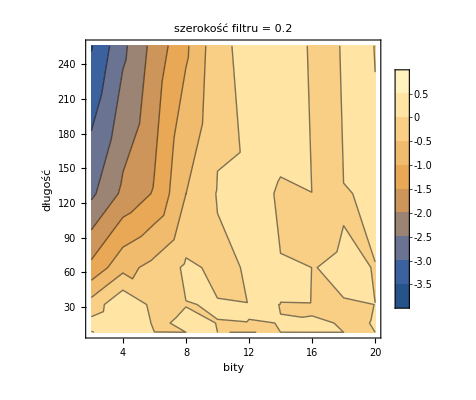
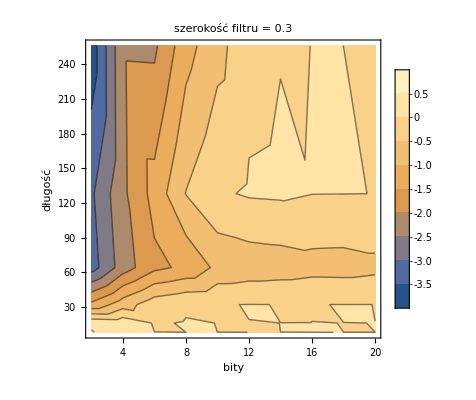
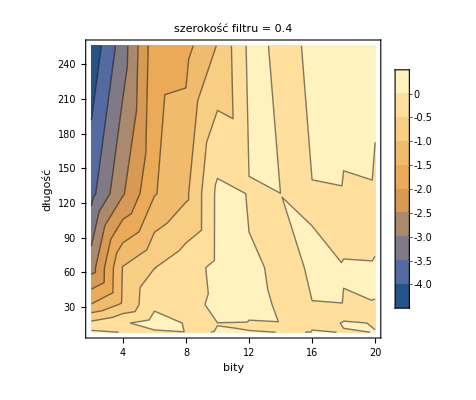
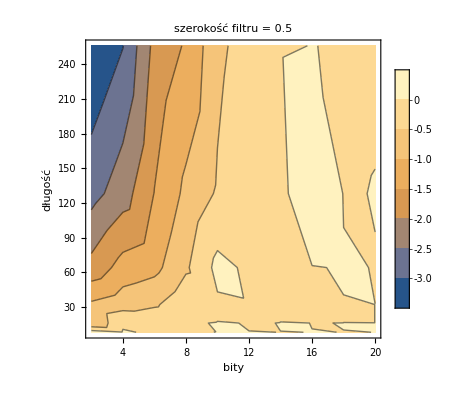
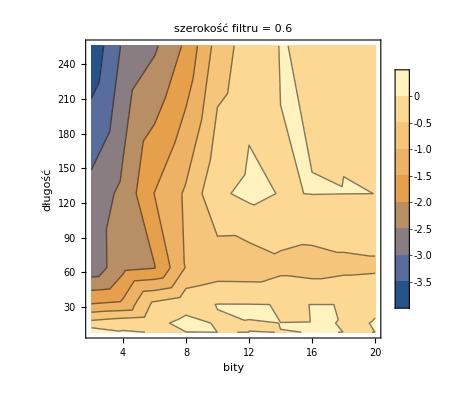
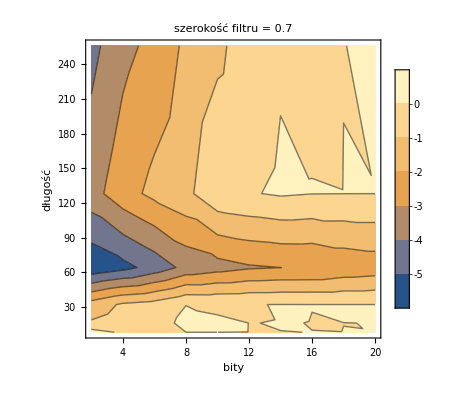
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[perSNR=Select[results,#[[2]]==i/2.0&][[All,{1,3,4}]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@perSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"bity","długość"},PlotLabel->"szerokość filtru = "<>ToString[i]],{i,perc}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

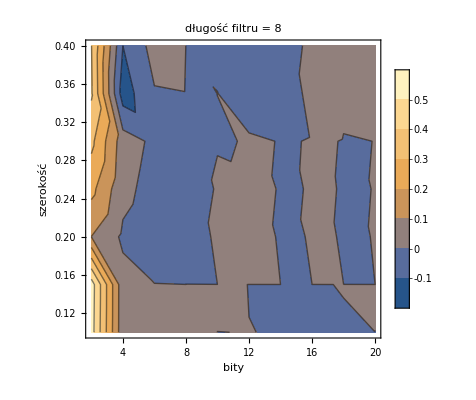
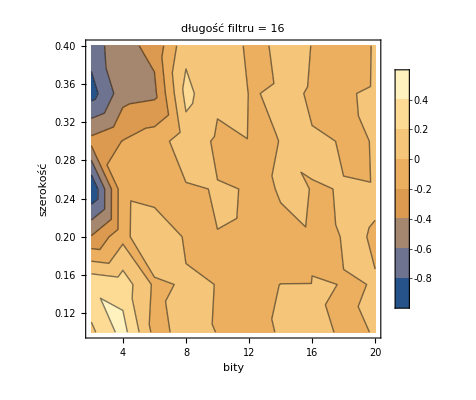
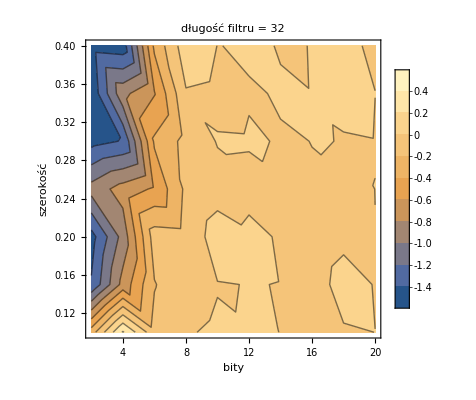
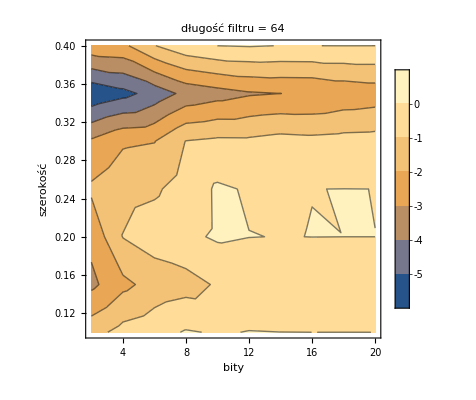
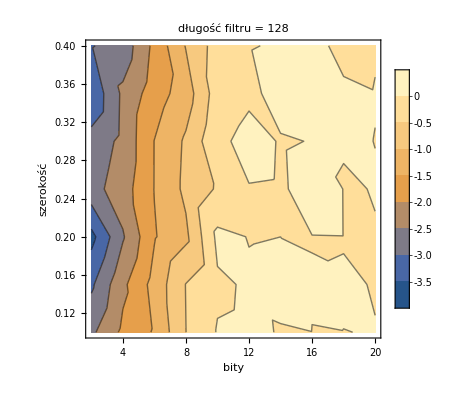
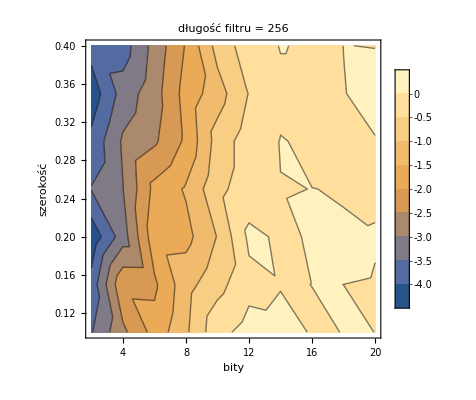
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[lenSNR=Select[results,#[[1]]==i&][[All,2;;]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@lenSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"bity","szerokość"},PlotLabel->"długość filtru = "<>ToString[i]],{i,len}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

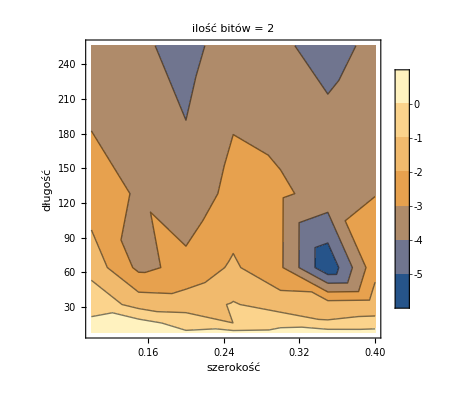
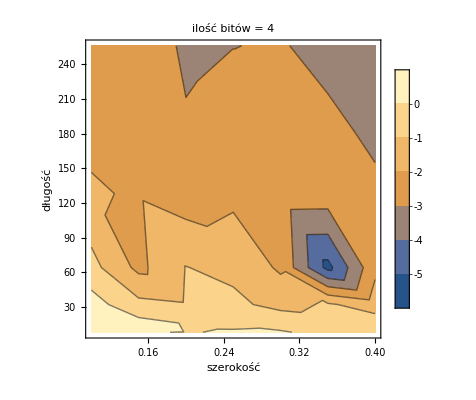
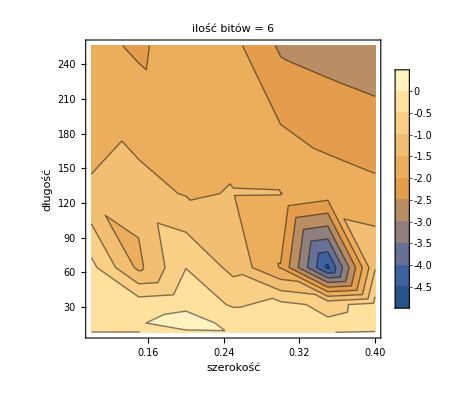
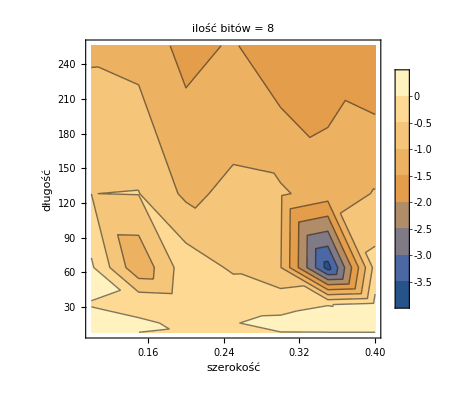
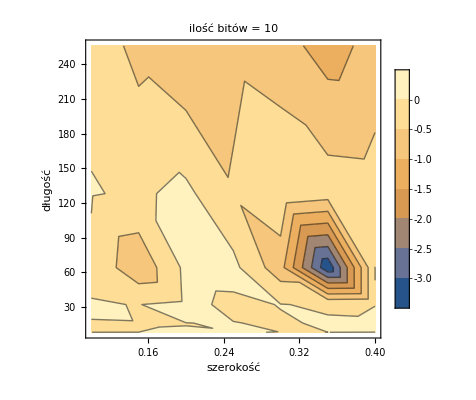
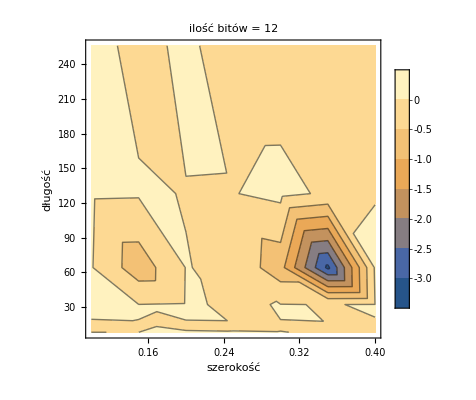
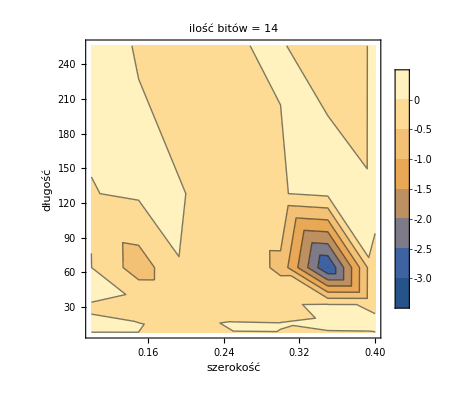
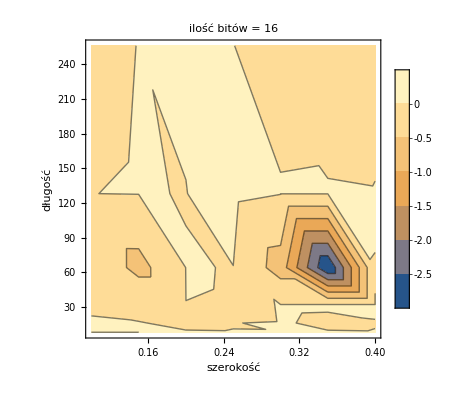
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[perSNR=Select[results,#[[3]]==i&][[All,{1,2,4}]];
ListContourPlot[{#[[2]],#[[1]],-Mean[#[[3]]][[-1]][[2]]+Mean[#[[3]]][[-1]][[1]]}&/@perSNR,PlotLegends->Automatic,PlotRange->Full,FrameLabel->{"szerokość","długość"},PlotLabel->"ilość bitów = "<>ToString[i]],{i,bb}],2],BaseStyle->ImageSizeMultipliers->1,ItemSize->Full]
```

```mathematica
spectrumPerf=Abs@Fourier[signalPerf, FourierParameters->{-1, 1}];
DiscretizeData[x_,bits_]:=Module[{max},max=Max[x]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] (*max/(Power[2,bits-1]-1)*) &/@x];
RoundData[x_,bits_]:=Round[x,2^-bits];
SpectrumError[spectrum_]:=Sqrt[Total[Abs[(spectrum-spectrumPerf)]^2]/((Total[Abs[spectrum]^2] ) )];
```